# Лабораторная 5. Операторы цикла и подпрограммы

Задание 1.  Для заданного натурального n изобразите график функции y=∑_(k=1)^n (Sin[x])^k (команды Sum и Plot). Как меняется график с изменением n? Сделайте мультипликацию (ListAnimate), показывающую изменение графика с ростом n.

```mathematica
n=15;
ListAnimate[Table[Plot[Sum[Sin[x]^i,{i,1,k}],{x,0,4*Pi},PlotRange->{-n,n}],{k,1,n}]]
```

```mathematica
n=15;
ListAnimate[Table[Plot[Sum[Sin[x]^i,{i,k}],{x,0,4Pi},PlotRange->n],{k,n}]]
```

Задание 2. Сформируйте список a из n=100 случайных целых чисел, лежащих в отрезке [-1000,1000] (команда RandomInteger). Составьте новый список, в который входят в точности положительные члены списка a (команды Delete, Append и Do или DeleteCases). 

Для чего нужна команда SeedRandom?

```mathematica
SeedRandom[1234];
a=RandomInteger[{-1000,1000},100];
b={};
Do[If[a[[i]]>0,AppendTo[b,a[[i]]]],{i,1,Length[a]}];
b
b2=DeleteCases[a,_?(!Positive[#]&)]
```

{795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}

{795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}

```mathematica
n=100;
SeedRandom[1234];a=Table[Random[Integer,{-10,10}],{n}]
b={};Do[If[a[[i]]>0,AppendTo[b,a[[i]]]],{i,n}];b
Print["Возможны более короткие способы (второй будет обсуждать позже):"]
b=Select[a,Positive]
b=Cases[a,_?Positive]
```

Задание 3.  Для заданного натурального n составьте матрицу, на главной диагонали которой стоят числа от 1 до n (Range, DiagonalMatrix),  а на соседних диагоналях --- числа от n-1 до 1. Найдите и изобразите (Eigenvalues, ConplexListPlot) собственные значения. Как меняется спектр при увеличении n?

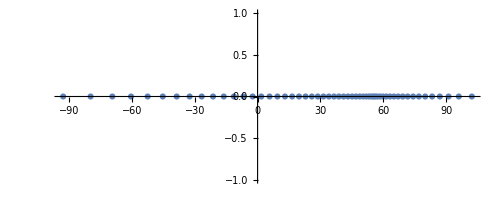

```mathematica
n=55;
a=DiagonalMatrix[Range[n]];
Do[a[[i+1,i]]=a[[i,i+1]]=n-i,{i,1,n-1}];

ei=Eigenvalues[a];
ComplexListPlot[ei]
```

```mathematica
n=55;a=DiagonalMatrix[Range[n]];
Do[a[[i+1,i]]=a[[i,i+1]]=n-i,{i,n-1}]
MatrixForm[a];
ei=Eigenvalues[a];
w=Transpose[{Re[ei],Im[ei]}];
ListPlot[w]
```

Задание 4. Напишите программу (оформленную как Module), находящую наибольшее в данном списке действительных чисел. Добавьте проверку того, что элементы списка действительно являются числами (используя четвертый аргумент команды If). Сравните с работой команды Max.

```mathematica
max[x0_List]:=Module[{maxx},maxx=x0[[1]];
Do[If[Not[NumberQ[x0[[i]]]],Print[x0[[i]]," не число."],If[x0[[i]]>maxx,maxx=x0[[i]]]],{i,1,Length[x0]}];
Print[maxx];
maxx]

test = {123, 4, 2134, 123, 123};
max[test]
```

2134

2134

```mathematica
x1=Table[Random[],{10}]
x1=Append[x1,3+I]
max[x0_]:=Module[{x=x0,maxx},maxx=x0[[1]];
Do[If[Not[NumberQ[x[[i]]]],Print[x[[i]]," не число."]];If[x[[i]]>maxx,maxx=x[[i]]],{i,1,Length[x]}];Print["max=",maxx]]
max[x1]
```

Задание 5. Запрограммируйте вычисление HeavisidePi(x) с помощью команды Piecewise. Проверьте результат путем построения графика.

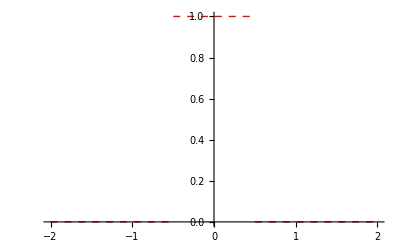

```mathematica
HeavisidePiCustom[x_]:=Piecewise[{{1,Abs[x]<1/2},{0,Abs[x]>1/2}}]
Plot[HeavisidePiCustom[x],{x,-2,2},PlotStyle->{Red,Thick,Dashed}]
```

Задание 6. Найдите первое из чисел последовательности x_n=Sin[n], для которого |x_n|<10^-4  (используйте команду While). Выведите на печать соответствующее n.

```mathematica
n=1;
While[Abs[Sin[n]]≥10^(-4),n++];
Print[n,"  ",N[Sin[n]]]
```

355  -0.0000301444

Задание 7. Вычислите e^-20.5 путем подстановки x=-20.5 в ряд Маклорена для экспоненты. Сравните результат с 1/e^20.5 . Чем объяснить расхождение?

```mathematica
x=-20.5;
maclaurin=Sum[x^i/i!,{i,0,100}]//N
direct=Exp[x]//N
alternative=1/Exp[-x]//N
```

1.81513×10^-8

1.25015×10^-9

1.25015×10^-9

```mathematica
x=-20.
Sum[(x)^i/(i!),{i,0,10000}]
Exp[x]
1/Exp[-x]
```

Задание 8. Интегральным оператором Фредгольма называют оператор (Ku)(x)=∫_a^b k(x,y)u(y)ⅆy. Функцию k называют его ядром. Ядро произведения K=K_1K_2 двух операторов Фредгольма находят по формуле k[x,y]=∫_a^b k_1(x,t)k_2(t,y)ⅆt.   Напишите программу (оформленную как Module) вычисляющую ядро произведения двух операторов Фредгольма. Как проверить правильность работы программы?

```mathematica
KernelFredholm[k1_,k2_,a_,b_]:=Module[{x,y,t},Function[{x,y},Evaluate[Integrate[k1[x,t]*k2[t,y],{t,a,b}]]]]
k=Function[{x,y},x*y];
k2=KernelFredholm[k,k,0,1];
k2[x,y]
```

-6.83333 y

```mathematica
KernelF[k1_,k2_,k_,a_,b_]:=Module[{x,y},k[x_,y_]=Integrate[k1[x,t]*k2[t,y],{t,a,b}]];

k[x_,y_]=x*y
a=0;b=1;
KernelF[k,k,k2,a,b];
k2[x,y]
```

Задание 9. Интегральным оператором Вольтерра называют оператор (Ku)(x)=∫_a^x k(x,y)u(y)ⅆy. Функцию k называют его ядром. Ядро произведения K=K_1K_2 двух операторов Вольтерра находят по формуле k[x,y]=∫_x^y k_1(x,t)k_2(t,y)ⅆt.   Напишите программу (оформленную как Module) вычисляющую ядро произведения двух операторов Вольтерра.

```mathematica
KernelVolterra[k1_,k2_]:=Module[{x,y,t},Function[{x,y},Evaluate[Integrate[k1[x,t]*k2[t,y],{t,y,x}]]]]
k=Function[{x,y},x*y];
k3=KernelVolterra[k,k];
k3[x,y]
```

-20.5 y (-2871.71-y^3/3)

Задание 10. Выведите на экран первые 4 члена последовательности z_1=1+x, z_(n+1)=1+√z_n. Используйте команду For.

```mathematica
For[z=1+x;Print["z1 = ",z];n=1,n<4,n++,z=1+Sqrt[z];
Print["z",n+1," = ",z]]
```

z1 = -19.5

z2 = 1.+4.41588 ⅈ

z3 = 2.66248+1.3281 ⅈ

z4 = 2.67896+0.395512 ⅈ

Задание 11. Последовательность z_n удовлетворяет разностному уравнению z_(n+1)=1+z_n-z_(n-1) и   начальным условиям z_0=2 и z_1=1. Постройте график первых 20 членов, вычислите их произведение (Product).

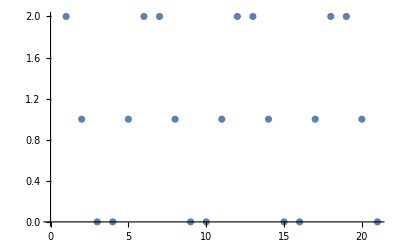

0

```mathematica
Clear[z];
z[0]=2;
z[1]=1;
Do[z[n]=1+z[n-1]-z[n-2],{n,2,20}];
ListPlot[Table[z[i],{i,0,20}]]
Product[z[i],{i,0,20}]
```

Задание 12. Схема Горнера вычисления многочлена b_0+b_1 x+...+b_mx^m может интерпретироваться как значение решения s_0 неоднородного разностного уравнения s_(i-1)=x*s_i+b_(i-1), i=m, m-1, ..., 1, с начальным условием s_m=b_m. Напишите  программу (оформленную как Module), вычисляющую значение многочлена в заданной точке x по списку его коэффициентов.

```mathematica
horner[a_,x_]:=Module[{m=Length[a]+1},
s=a[[m+1]];
Do[s=a[[i+1]]+s*x,{i,m-1,0,-1}];s]

m=5
a=Table[Subscript[b,i],{i,0,m}];
horner[a,m,x]//Expand
```

```mathematica
horner[a_List,x_]:=Module[{s,m},m=Length[a];s=a[[m]];
Do[s=a[[i]]+s*x,{i,m-1,1,-1}];
s]

coef=Table[Subscript[b,i],{i,0,5}];
horner[coef,x]//Expand
```

{795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}_0-20.5 {795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}_1+420.25 {795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}_2-8615.13 {795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}_3+176610. {795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}_4-3.62051×10^6 {795,38,765,924,580,61,909,217,6,509,246,425,552,102,712,346,735,522,230,175,196,711,261,636,844,720,114,732,659,637,41,519,376,100,275,715,730,834,911,211,81,508,326,460,793,778,762,340,10,744,182,922,26,330,436,349,482,402,425}_5